# Bee Thermodynamics

This worksheet take the bumblebee thermodynamic model and reparameterizes it into a dimensionless form.

## The model (for a flying bumblebee with no behavioural cooling)

The thermodynamic heat equation for the model is given by

```mathematica
heatEqn = D[Tth, t] == Q/Subscript[m, th]/c;
```

where m_th is the mass of the bee’s thorax (kg), c is the specific heat capacity of the thorax (J kg^-1 K^-1), Tth is the temperature of the thorax (K), and Q is the total rate of heat production by the thorax (J s^-1).

Q can be decomposed into several terms

```mathematica
Q:=Qs + Qr1 - Qr2 - Qc + Qi + Qh
```

Qs is the heat from the solar radiation (J s^-1), Qr1 and Qr2 is the incoming and outgoing heat, respectively, from thermal radiation (J s^-1), Qc is the heat loss due to convection (J s^-1) and Qi is the heat from an individual's metabolism (J s^-1), and and Qh is the heat transferred from the thorax to the head and lost through the head (J s^-1).

At equilibrium the right-hand side of the heat equation is zero, meaning the Q=0, and therefore the five terms of Q must balance. This means that at thermal equilibrium 

Qs+Qr1+Qi+Qh = Qr2+Qc

### Solar Radiation

```mathematica
Qs=Subscript[ϵ, a] Subscript[a, th] P(Subscript[α, point]+Subscript[α, nonpoint] f);
```

Qs is the solar radiation, P is the incoming flux of solar radiation (J s^-1 m^-2), a_th is the surface area of the thorax (roughly 4.5 x 10^-5 m^2) , ϵ_a is the bee’s absorptivity (=0.91), α_point (=0.25) is the fraction of the bee’s surface that is exposed to the solar radiation,  α_nonpoint (=0.5) is the fraction of the bee’s surface that is exposed to non point sources of solar radiation, and f (=0.25) is the fraction of solar radiation that is reflected from the surface of the Earth.

### Thermal Radiation

Qr1 and Qr2 are the thermal radiation terms which correspond to incoming radiation from the atmosphere, the ground

```mathematica
Qr1 = Subscript[α, nonpoint] Subscript[ϵ, a] Subscript[a, th](δ Tair^6+σ Tg^4);
```

and outgoing radiation from the bee

```mathematica
Qr2=Subscript[ϵ, e] σ Subscript[a, th] Tth^4;
```

where α_nonpoint (=0.5) is the fraction of the bee’s surface that is exposed to non point sources of solar radiation , Tair is the temperature of the air, Tg is the temperature of the ground, Tth is the temperature of the bee’s thorax (all temperature are in Kelvin), σ is the Stefan-Boltzmann constant (=5.67x 10^-8 J s^-1 m^-2 K^-4), δ is a constant still to be full described (= 5.31x 10^-13 J s^-1 m^-2 K^-6), and ϵ_e=0.97 is the emissivity of honeybee.

### Convection

```mathematica
Qc=Subscript[a, th] h(s Tth-Tair);
```

where h (J s^-1 m^-2 K^-1) is a constant that depends upon the environmental conditions  h := c_d κ / d_th (v d_th/ν)^n

and κ is the thermal conductivity of the air (J s^-1 m^-1 K^-1), ν is the kinematic viscosity of the air, d_th is the average diameter of the thorax (m),  and n, c_dare unitless constants estimated from data (for bumblebees n=1.975485 (unitless) and c_d=2.429809 x10^-7 (unitless)).

### Metabolism

An individuals metabolic rate is a function of body mass and body temperature.

```mathematica
Qi = Subscript[a, met] Exp[-Subscript[b, met] (1/Tth - 1/T0)];
```

where a_met = i0 (m_b/m0)^(3/4) , b_met=Eact/k and i0 is a normalisation constant (the metabolic rate at temperature T0 and weight m0), m_b is the body mass of the bee, Eact =0.63 eV (= 1.0093 × 10^-19 J ) is the activation energy, k is Boltzmann’s constant (=8.617 x 10^-5 eV K^-1 =  1.3806 x 10^-23 J K^-1) and Tth is the temperature of the thorax (K).

### Head Cooling

Heat is also transferred between the head and thorax.

```mathematica
Qh= Subscript[ϵ, a] Subscript[a, h] P(Subscript[α, point]+Subscript[α, nonpoint] f) + Subscript[α, nonpoint] Subscript[ϵ, a] Subscript[a, h](δ Tair^6+σ Tg^4) - Subscript[ϵ, e] σ Subscript[a, h](Tth-ΔTh)^4-Subscript[a, h] h(s (Tth-ΔTh)-Tair);
```

where  ΔTh is the difference in temperature between the head and thorax, a_h is the surface area of the head, and all other parameters are as described above.

### Parameterisation

Set  parameter values for a  flying bumblebee

```mathematica
(* Most of the parameters or relationships are set here *)
params={ Subscript[m, b]-> 0.149 10^-3,(* Mass of bee, kg *)
Subscript[m, th]->0.057 10^-3, (* Mass of thorax, kg *)
δ-> 5.31 10^-13,  (* Default value 5.31 E-13 *)
f-> 0.25,             (* dimensionless *)
Subscript[α, nonpoint]-> 0.5 ,        (* dimensionless *)
Subscript[α, point]-> 0.25 ,        (* dimensionless *)
c-> 3.349 10^3, (* Specific heat capacity of bee tissue   J K^-1 kg^-1  *)
Subscript[a, th]->9.3896 10^-5,  (* Surface area of the thorax default value 9.3896 E-5 , m^-2*)
Subscript[ϵ, e]-> 0.97,          (* Emissivity of the thorax    dimensionless *)
Subscript[ϵ, a]-> 0.935,         (* Absorptivity of the thorax   dimensionless *)
n-> 1.975,         (* dimensionless *)
v->2.1,              (* Flight speed m s^-1  (default 4.1) *)
Subscript[c, d]-> 2.43 10^-7,          (* dimensionless *)
Subscript[d, th]-> 2 (Subscript[a, th]/π)^(1/2),  (* diameter of thorax  m  *)
i0->0.06404973, (* Metabolic power (W = J s^-1) of a bee of mass m0 at temp T0 (fitted value 0.06404973)  (lowest value 0.001349728) *)
 m0->0.177 10^-3 ,  (* reference Mass [kg] of a full bee 177 mg *)
 T0 -> 25+ 273.15 ,    (* Temperature for metabolic rate corresponding to i0  *)
τ-> 1,                       (* Time scale, s *)          
Eact-> 0.63 1.6022 10^-19,        (* Activation energy (fitted value 0.009176471*1.6022*10^-19) J. Default 0.63 eV *)
s -> 0.9965     (* ratio of surface temperature to internal temperature (thorax) in K (default 0.9965)*)
};
```

```mathematica
constants ={
k-> 1.3806 10^-23, (* Boltzmann constant  J K^-1 *)
σ-> 5.67 10^-8      (* Stefan-Boltzmann constant W m^-2 K^-4 *)
};
```

Set environmental values

```mathematica
(* Now the environmental parameters *)
envParams={
Tair-> 15+273.15,  (* Kelvin *)
Tg-> 17.1+273.15,       (* Kelvin *)
P-> 332.3878,             (*  W m^-2 *)
Pr-> 1.013 10^5,  (* atmospheric pressure, N/m^2) *)
Subscript[R, specific]-> 287.058, (* J/kg/K *)
κ-> (0.02646 Tair^1.5) /(Tair + 245.4 10^(-12/Tair)) ,    (* Thermal conductivity of air  J s^-1 m^-2 K^-1  *)
μ-> (1.458 10^-6  Tair^1.5)/(Tair+110.4),(* Dynamic viscosity   *)
ρ-> Pr/Subscript[R, specific], (* in humid air at sea level *)
ν -> μ/ρ (* Kinematic viscosity m^2 s^-1   *)
};
```

## Non-dimensional version of the thorax only model

Here we rewrite the model (with Qh=0) in terms of non-dimensional quantities.

All temperatures will be w.r.t. a reference temp T0, and a timescale τ

#### Heat equation

```mathematica
heatEqnND := x'[y] == Q2;
```

the dimensionless variables are

```mathematica
heatEqnVars = {x->Tth/T0,
y->t/τ}
```

{x→Tth/T0,y→t/τ}

and the terms Q2 is

```mathematica
Q2 := QiND+QsND;
```

#### Metabolic heat production (Qi term)

```mathematica
QiND = K1 Exp[-K2 (1/x - 1)];
```

#### Direct solar radiation, thermal radiation and convection

```mathematica
QsND=K3 + K4 x + K5 x^4;
```

the dimensionless constants are

```mathematica
QParams={
K1-> i0 (Subscript[m, b]/m0)^(3/4)τ/(T0 Subscript[m, th] c), (* Metabolic part *)
K2->Eact/(k T0),  (* Metabolic part *)
K3->(τ Subscript[a, th]/T0) (Subscript[ϵ, a](Subscript[α, point] P + Subscript[α, nonpoint](P f + δ Tair^6+σ Tg^4))+ Subscript[c, d] κ (v/ν)^n (Subscript[d, th])^(n-1) Tair)/(Subscript[m, th] c), (* Mixture of parts *)
K4-> -Subscript[a, th] Subscript[c, d] κ (v/ν)^n (Subscript[d, th])^(n-1) s τ/(Subscript[m, th] c), (* Convection part *)
K5->-Subscript[ϵ, e]σ Subscript[a, th] τ T0^3/( Subscript[m, th] c)     (* Thermal radiation part  *)
};
```

```mathematica
{K1->(i0 τ (Subscript[m, b]/m0)^(3/4))/(T0 c Subscript[m, th]),K2->Eact/(k T0),K3->(τ Subscript[a, th] ((Tair κ (v/ν)^n Subscript[c, d] Subscript[d, th]^(-1+n))/T0+(Subscript[ϵ, a](Subscript[α, point] P + Subscript[α, nonpoint](Pf + δ Tair^6+σ Tg^4)))/T0))/(c Subscript[m, th]),K4->-(κ (v/ν)^n τ Subscript[a, th] Subscript[c, d] Subscript[d, th]^(-1+n)s)/(c Subscript[m, th]),K5->-(T0^3 σ τ Subscript[a, th] Subscript[ϵ, e])/(c Subscript[m, th])}
```

{K1→(i0 τ (m_b/m0)^(3/4))/(c T0 m_th),K2→Eact/(k T0),K3→(τ a_th ((Tair κ (v/ν)^n c_d d_th^(-1+n))/T0+(((Pf+Tair^6 δ+Tg^4 σ) α_nonpoint+P α_point) ϵ_a)/T0))/(c m_th),K4→-(s κ (v/ν)^n τ a_th c_d d_th^(-1+n))/(c m_th),K5→-(T0^3 σ τ a_th ϵ_e)/(c m_th)}

Display the final non-dimensional version of the model.

```mathematica
heatEqnND
```

x'[y]==ⅇ^(-K2 (-1+1/x)) K1+K3+K4 x+K5 x^4

Note: one further parameter could be removed (one of K1, K3, K4 and K5) by scaling the time scale appropriately.

## Numerical solution of the heat equation

### Numerical integration

Define differential equation

```mathematica
eqn1 =Q2/.{x->x[y]}/.QParams //.params /.constants//.envParams ;
eqn := x'[y]==eqn1;
eqn
```

x'[y]==396.135+0.000989014 ⅇ^(-24.5219 (-1+1/x[y]))-408.447 x[y]-0.000716995 x[y]^4

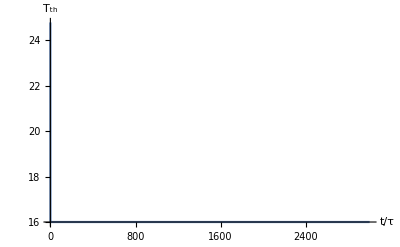

```mathematica
sol=NDSolve[{eqn,x[0]==1},x,{y,0,5000}, Method-> "Automatic"];
Plot[Evaluate[x[y]*T0-273.15/.sol/.params],{y,0,3000},PlotRange->All, AxesLabel->{t/τ, Subscript[T, th]}]
```

### Numerically solve for equilibrium

Now numerically solve for the equilibrium value

```mathematica
Qsub = Q2 /.QParams//.params//.envParams/.constants
xEquilib = NSolve[Qsub==0, x, Reals]
```

396.135+0.000989014 ⅇ^(-24.5219 (-1+1/x))-408.447 x-0.000716995 x^4

{{x→-504.793},{x→0.969856},{x→2.14562},{x→491.381}}

Write equilibria in degrees C

```mathematica
x*T0 - 273.15 /. xEquilib/.params
```

{-150777.,16.0125,366.568,146232.}

### Stability of the equilibria

Calculate the derivative of Q2 w.r.t. x at the equilibrium value. 

For the solution to be stable this should be negative

```mathematica
D[Q2,x]/.xEquilib /.QParams//.params//.envParams/.constants
```

{372958.,-408.438,2149.63,-336419.}

## ReplaceAll::reps: "{x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."